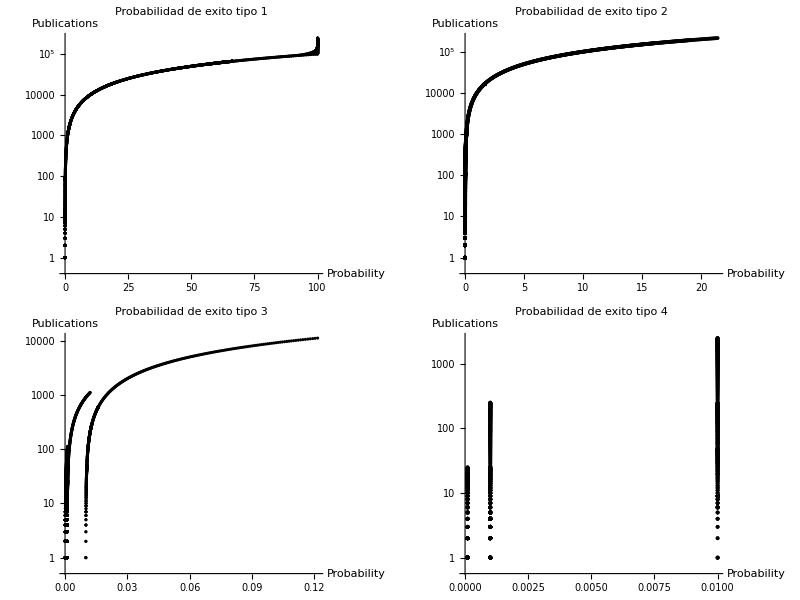

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
x = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory[y<>"/images"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/prob-pub-1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-5-1.0E-4-curve.csv"];
pub7= Import[x<>"/averageResults/prob-pub-1-0.01-100-true-curve.csv"];
pub8= Import[x<>"/averageResults/prob-pub-1-0.001-100-true-curve.csv"];
pub9= Import[x<>"/averageResults/prob-pub-1-1.0E-4-100-true-curve.csv"];
pub10= Import[x<>"/averageResults/prob-pub-5-0.01-100-true-curve.csv"];
pub11 = Import[x<>"/averageResults/prob-pub-5-0.001-100-true-curve.csv"];
pub12 = Import[x<>"/averageResults/prob-pub-5-1.0E-4-100-true-curve.csv"];
plotPub1= Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 , pub7, pub8, pub9, pub10, pub11, pub12},ImageSize->600,  AxesLabel->{"Probability","Publications"}, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 1",PlotStyle->{{Thick,Black}}]];

Export["prob-pub-1.png",plotPub1];

pub13= Import[y<>"/averageResults/prob-pub-2-0.01-curve.csv"];
pub14= Import[y<>"/averageResults/prob-pub-2-0.001-curve.csv"];
pub15= Import[y<>"/averageResults/prob-pub-2-1.0E-4-curve.csv"];
pub16 = Import[y<>"/averageResults/prob-pub-6-0.01-curve.csv"];
pub17 = Import[y<>"/averageResults/prob-pub-6-0.001-curve.csv"];
pub18 = Import[y<>"/averageResults/prob-pub-6-1.0E-4-curve.csv"];
pub19= Import[x<>"/averageResults/prob-pub-2-0.01-100-true-curve.csv"];
pub20= Import[x<>"/averageResults/prob-pub-2-0.001-100-true-curve.csv"];
pub21= Import[x<>"/averageResults/prob-pub-2-1.0E-4-100-true-curve.csv"];
pub22= Import[x<>"/averageResults/prob-pub-6-0.01-100-true-curve.csv"];
pub23 = Import[x<>"/averageResults/prob-pub-6-0.001-100-true-curve.csv"];
pub24 = Import[x<>"/averageResults/prob-pub-6-1.0E-4-100-true-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6, pub7, pub8, pub9, pub10, pub11, pub12 },ImageSize->600,  AxesLabel->{"Probability","Publications"}, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 2", PlotStyle->{{Thick,Black}}]];
Export["prob-pub-2.png",plotPub2];

pub25= Import[y<>"/averageResults/prob-pub-3-0.01-curve.csv"];
pub26= Import[y<>"/averageResults/prob-pub-3-0.001-curve.csv"];
pub27= Import[y<>"/averageResults/prob-pub-3-1.0E-4-curve.csv"];
pub28 = Import[y<>"/averageResults/prob-pub-7-0.01-curve.csv"];
pub29 = Import[y<>"/averageResults/prob-pub-7-0.001-curve.csv"];
pub30 = Import[y<>"/averageResults/prob-pub-7-1.0E-4-curve.csv"];
pub31= Import[x<>"/averageResults/prob-pub-3-0.01-100-true-curve.csv"];
pub32= Import[x<>"/averageResults/prob-pub-3-0.001-100-true-curve.csv"];
pub33= Import[x<>"/averageResults/prob-pub-3-1.0E-4-100-true-curve.csv"];
pub34= Import[x<>"/averageResults/prob-pub-7-0.01-100-true-curve.csv"];
pub35 = Import[x<>"/averageResults/prob-pub-7-0.001-100-true-curve.csv"];
pub36 = Import[x<>"/averageResults/prob-pub-7-1.0E-4-100-true-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6, pub7, pub8, pub9, pub10, pub11, pub12 },ImageSize->600,  AxesLabel->{"Probability","Publications"},PlotRange->All,PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 3",PlotStyle->{{Thick,Black}}]];
Export["prob-pub-3.png",plotPub3];

pub37 Import[y<>"/averageResults/prob-pub-4-0.01-curve.csv"];
pub38= Import[y<>"/averageResults/prob-pub-4-0.001-curve.csv"];
pub39= Import[y<>"/averageResults/prob-pub-4-1.0E-4-curve.csv"];
pub40 = Import[y<>"/averageResults/prob-pub-8-0.01-curve.csv"];
pub41 = Import[y<>"/averageResults/prob-pub-8-0.001-curve.csv"];
pub42 = Import[y<>"/averageResults/prob-pub-8-1.0E-4-curve.csv"];
pub43= Import[x<>"/averageResults/prob-pub-4-0.01-100-true-curve.csv"];
pub44= Import[x<>"/averageResults/prob-pub-4-0.001-100-true-curve.csv"];
pub45= Import[x<>"/averageResults/prob-pub-4-1.0E-4-100-true-curve.csv"];
pub46= Import[x<>"/averageResults/prob-pub-8-0.01-100-true-curve.csv"];
pub47 = Import[x<>"/averageResults/prob-pub-8-0.001-100-true-curve.csv"];
pub48 = Import[x<>"/averageResults/prob-pub-8-1.0E-4-100-true-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6, pub7, pub8, pub9, pub10, pub11, pub12 },ImageSize->600,  AxesLabel->{"Probability","Publications"}, PlotRange->All, PlotRange->All,PlotLabel-> "Probabilidad de exito tipo 4",PlotStyle->{{Thick,Black}}]];
Export["prob-pub-4.pdf",plotPub4];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["prob-pub-totalModels.pdf",pubTotal];
```